Observed median difference: 0.00170514

Histogram of permuted median difference:

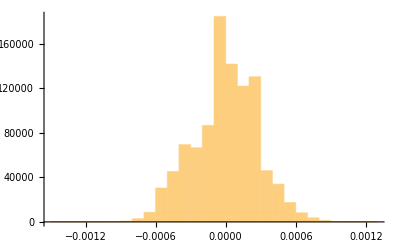

p-value: 0.

```mathematica
(* Given two lists, perform permutation test to check if the median is the same, i.e., find p-value *)


NBoot=1000000; (* number of permutation to do *)

(* list assumed to have larger median *)
list1={0.011005959868538997,0.004879774792808037,0.004854806693528387,0.0034118824400312755,0.005138328314262981,0.004011213657098273,0.011065322950932162,0.0028874165858143847,0.0011126786143840826,0.0021873409212511082,0.003144227411512141,0.0026781652478057773,0.0016595609675270717,0.0005635745363913635,0.001725668583532339,0.002381106245727632,0.0024908175184385297,0.003262450778250853,0.0010944314770135186,0.0035979323296805115,0.007496016094026105,0.0005070593373443077,0.006756830358077744,0.0024727991254326225,0.0008439975110190851,0.0022169352446448232,0.0006736537657079054,0.002655526155760042,0.014365216106715187,0.0015685465878868183,0.003952274362528751,0.0006160713765936778,0.0007026947289556614,0.0014649666815357947,0.0010229951042969173,0.003060029971118736,0.0016550157986458848,0.0007339963295774103,0.0019145195582763125,0.002331223071519888,0.006697652996123258,0.0008712729511023878,0.0034277853971653857,0.0045396553070811045,0.0017804170767097085,0.00206785169766347,0.0032443781494316233,0.00168898235883967,0.001896620812119146,0.0020984578554253735,0.0014785023183638442,0.003462728187069419,0.0036281248687051026,0.00199464072013044,0.0023315218750904355,0.0006234304086120146,0.0015648813595239542,0.0036537074656994586,0.0009082926244659683,0.0012679563295257324,0.0017011906909444809,0.004053273112305313,0.002186249724662543,0.002687981364633113,0.004705933578380967,0.001583685227648019,0.002385661340444315,0.002263903245082169,0.0030780867381558926,0.002703531856547863,0.004226173431387719,0.008360762027238804,0.014997897440427756,0.0032522848382251,0.0064430991475054366,0.022384091871875404,0.00447434773103788,0.00040631242993473585,0.003498823074138063,0.006185106418999463,0.0035668225525133674,0.0009178286741578651,0.0009468864517204366,0.0013375819039491814,0.002581268355054685,0.0010676734257400386,0.0006751422700893321,0.001719661931302649,0.004124857012535869,0.010128839526358069,0.003113876909261237,0.002034242965451316,0.004659332955922521,0.012044851297514736,0.0030392025174325902,0.004193347901253619,0.0052006853396798286,0.0016179968660439816,0.005115612716424226,0.003915488338596725,0.007706458106255838,0.0006322471559904125,0.0016456478364303793,0.005832295436601618,0.004010312965806758,0.004138240791327563,0.0013134205237306958,0.017466100402271267,0.006497286165974111,0.0022475244262392838,0.0018118858491044654,0.06721291624994548,0.006834685719992252,0.0024433612825555968,0.0012455970362678563,0.011176341200682722,0.0009980780465258699,0.004179010068413617,0.001208463038667569,0.0010613595530799456,0.0014166381799626886,0.00532490518843477,0.0030913615935642402,0.003980238651989174,0.014891814039117645,0.001255129789858164,0.001215529671958724,0.0016751581746296473,0.011782173838950015,0.004395916909069264,0.0006976044815748617,0.00559790771456615,0.0008159411187804216,0.002265528174630772,0.003450021597974138,0.002370138761145489,0.006026763173878928,0.003640576720473287,0.0011156501902620053,0.0008961463542677921,0.003344542070479226,0.001383400999737521,0.0013640410398417626,0.0009500007845719937,0.0029281400627537216,0.0018433382824219668,0.0019259170464091529,0.001185516290193223,0.0010566002820541801,0.0060440386527907015,0.006652526005750196,0.015240754955986419,0.0008640439419192289,0.0023782000219583653,0.0013538276722823452,0.0021612606338529423,0.0034131842088643955,0.005238868322078198,0.008580032683567919,0.01516457717314115,0.0015794538365092147,0.006703113914355953,0.0036946144481364057,0.0030993748868043463,0.002604662750751738,0.001209707742414573,0.00216285943317819,0.00438843471949893,0.0019348423968064477,0.001042098358624927,0.0030318782828738402,0.007688921476055697,0.0007606301228492447,0.004937946023530487,0.0017148472796317067,0.004051472476097118,0.0010253422432809718,0.0028165310938545575,0.0012004876496105972,0.0025987608753801532,0.002850352528062034,0.0019473206959465478,0.005091901167350861,0.00789140805802454,0.0008797188290766208,0.0020477872308804243,0.00966361590170994,0.0008387763726043565,0.00020464182034056868,0.020544968438743618,0.0012746252566368022,0.0013214117240088032,0.0027088410619592472,0.0013086711725830706,0.0049067235745021654,0.0011273222923410997,0.0028481123082698856,0.002459444145676755,0.0012191865191067289,0.0005469951468903656,0.0036920131841046877,0.010628136056642408,0.004503884158990291,0.011406764905972077,0.005844821013772244,0.002634602202784016,0.005557388955132678,0.006017633250239463,0.005370357138793754,0.0033011397384819833,0.007748123066412169,0.0008445974557862918,0.003177352469905076,0.02069958108879323,0.0021358915252186507,0.0005348860664366522,0.004577057510976212,0.010437595227458489,0.0017943921519536913,0.007886936636802526,0.0013887857964799495,0.005449140014494392,0.01931529927485571,0.017031380841850005,0.0052522629332371895,0.00910454504850056,0.004239488449399177,0.008780607712433518,0.0013193308071840764,0.006699867638438521,0.0011974023477700352,0.008315955190559148,0.008288837256941106,0.00391824698719777,0.010106356414620696,0.043789466080646516,0.0007073207033709194,0.004239649411903869,0.0034236115030068,0.0012799592971508183,0.0035080304967049104,0.002227683454499833,0.002918103007336443,0.010949484234324009,0.005132003338867123,0.005576854117804121,0.004203682268282398,0.0014937095637601102,0.001135284323777402,0.0037918332567838074,0.0016546742493881122,0.004836568179544137,0.01635864364628827,0.0034550910251245235,0.002947273079192085,0.0018331833830736626,0.009021187835317046,0.005208359338199686,0.0007451953940884508,0.0039062242275872796,0.008805342831074876,0.04230722656276155,0.02086035871382943,0.004076449564868133,0.011776553379346303,0.010510578283595829,0.0048648581675735355,0.007142326433710578,0.004769787441310764,0.00784562938772293,0.008056303373675654,0.0030690823471149456,0.005982150444501854,0.0037435247731282388,0.0035885104435279995,0.002222087982388691,0.0033522472611542337,0.0024623318973834097,0.009100502685837432,0.008122990101807975,0.017390103647765998,0.0038592881614668583,0.007641441171205231,0.014555241124536546,0.003924929672713364,0.006879351071777947,0.00412658916419591,0.007298629684255647,0.006627163329763643,0.007726263046140391,0.0037822747662619154,0.0066869816142941406,0.005307128092538724,0.005192088144284015,0.0064389894062215096,0.005249325136939061,0.013461520755413747,0.0055471308584684985,0.004602748435003413,0.02048814896166738,0.001304478175831853,0.008901450191473967,0.014449656670040945,0.005316047978843909,0.0033011094385026083,0.001988875926063449,0.01280522247738493,0.005378301447894296,0.0035072319329588625,0.006481261826981552,0.0036663380865679914,0.005807650987219641,0.022271224251836724,0.011028025122305423,0.0015423326060198942,0.004147635338983869,0.005768541857807814,0.035936792135155424,0.010113118361801931,0.027017347662794542,0.010094690397835684,0.010098865757216567,0.004807283356817513,0.005377754681356587,0.018028426908330654,0.00341441967421854,0.012112923868475622,0.008879173138699483,0.0014917629779185055,0.006836897610813472,0.008531787558335602,0.0066287877866384815,0.003877780759932503,0.0035046426544864794,0.0078094493790224345,0.0024923457655647995,0.012777433027494659,0.007377853880096122,0.003321724680028183,0.005569308767639288,0.006051861596938307,0.003695604891290557,0.009850619413935505,0.01594667640785603,0.009214094782158485,0.006414079362748411,0.008061065741475098,0.0030635291261852187,0.0056603058868811935,0.004701849224272604,0.003904823746072972,0.021224646013825853,0.011743198658895313,0.0026951144545181737,0.01665779428641825,0.011750876311972766,0.002362408316236068,0.002049024137316996,0.004681030776487961,0.009700705653070824,0.012523104929873938,0.0065601698831982925,0.002605262625490432,0.004925835123959903,0.005881046194020333,0.008834660708132228,0.010412691721453324,0.004806707661602836,0.004803618909558902,0.0036625468391313417,0.007573093593027961,0.002426052664543346,0.003983592152643545,0.003678784504582184,0.010610527865173506,0.0045564177648001565,0.005079471968564967,0.0059474599052493134,0.002322390677728295,0.004036476092356791,0.0038726556137981464,0.0031944236988974773,0.001218171149046927,0.0014580040148104926,0.005158968186183766,0.0017052690118991062,0.0038316374742559073,0.0635277492438017,0.0074576851784406055,0.008084927513027577,0.007314397624975547,0.004463725101760736,0.00529046699753191,0.004448404089907458,0.010270311361768944,0.008148393090537939,0.002037978783958675,0.0012124390293503002,0.008293554203557393,0.0218211207655818,0.0017885926098604942,0.005307780618772984,0.030276458226324222,0.0032409630118396455,0.005279125159867066,0.0023938326962529063,0.006352421910958457,0.0055949155889773615,0.0065625652631199445,0.011071896264245323,0.004395678027794277,0.012429173674482725,0.003485910545358316,0.009574791791191221,0.008919949820248168,0.010227228421335072,0.014740459100952041,0.02138502420769856,0.009140644981583016,0.014543188366385188,0.007709321158816003,0.006014046251363343,0.005600798961517247,0.004035589322613402,0.007087062860136102,0.0058944352535582846,0.008051614392847458,0.006713815575774484,0.003045802483031358,0.007142543922005082,0.00588990154261152,0.004075737338534083,0.0023082946659132215,0.007552032124010184,0.014991501875567453,0.017141766453087636,0.0024617871166417644,0.011822402131286776,0.006312386905209599,0.044761252909226085,0.010989219037130585,0.004315095376375789,0.010205761451887056,0.07098268353994337,0.007316682887326538,0.005401272893242078,0.009843281282445939,0.0025958701970088404,0.003850937425529245,0.0010768108763830055,0.003658442828502869,0.005012353761554319,0.005778220342511785,0.0017332981644368143,0.005560704169995113,0.005351371833111477,0.00253956744556011,0.014607622377934382,0.00228146494242322,0.01515265861768547,0.04934487249837577,0.007648486002830646,0.006247496622019856,0.02926733211920096,0.006648627074198206,0.0027028254459272073,0.0002865435828646467,0.00304705121697146,0.0026501949093415836,0.0032315439162537013,0.044300645296363135,0.021814503516441045,0.005457657691548939,0.03690373761786342,0.005274128124525042,0.011525237071704515,0.004898533351537948,0.006328512606134706,0.0032880090113500907,0.011370325908050226,0.002108445745067242,0.004016766907114727,0.010511227029910843,0.0036212454769059075,0.006110581269899025,0.0034581266692054443,0.008853939642290413,0.012954911155314271,0.01966123409198853,0.007591171146359658,0.012845774320211724,0.010681042549116653,0.004531326420861588,0.012981829872991053,0.031075638688612926,0.008877868162191887,0.03658477671597315,0.005833953323060048,0.003211966139992971,0.003276637334415143,0.017605663575167803,0.0034263810756919332,0.004762174301425635,0.008188630698531757,0.001953559106429789,0.006916944840368377,0.007117737898585887,0.004353002309585236,0.003417838176407965,0.012276063360564596,0.0020719471793449063,0.002850001586832044,0.00251888768378135,0.000560548196663383,0.00588149613889713,0.0036960476672709196,0.004427123741452578,0.005815657255905159};

(* list assumed to have smaller median *)
list2={0.003258301046332285,0.0055624480340875065,0.002625068463225631,0.0027590304567908677,0.002171173637240295,0.0016735707992957892,0.0021347008408258558,0.0014596305675714427,0.002447918601696067,0.0016166507330504685,0.002374968058134255,0.0022740363979844706,0.0003674906452142518,0.001970965578108771,0.0019609989752555554,0.00116848297345605,0.00033255822152211835,0.005790547220150257,0.005630626392637747,0.0036332176801079463,0.0022813337871990876,0.0004740533082233663,0.0033897568071291693,0.0014626145118287201,0.00045898229345218695,0.0024969214859630233,0.0005087423934956615,0.01244379374815473,0.004359193009420721,0.0012476929747766937,0.0007352360178387824,0.000565880438227205,0.0034285578581744504,0.0020050084018581804,0.001894045586070394,0.001989151739085022,0.0015425231711823442,0.00318147986881301,0.002337919534916197,0.0017573914372994482,0.0022991332398977125,0.006210395007377443,0.0040343749295456,0.004200112443964128,0.0008704497098278879,0.0009929034766199736,0.0018738723289273554,0.00272061204718762,0.0035292698728022188,0.004009478131622834,0.001385425039548687,0.004744715779497663,0.005536472787473432,0.0030084927460150212,0.0037883767887894886,0.00673930438596773,0.0018240159571313028,0.0019480935210343556,0.0015795303571396898,0.0013021768443801452,0.0008055932347824722,0.0037259513238046436,0.0018340848076069502,0.002252426727631209,0.0014565313517307583,0.002847758800579576,0.0020577698087220564,0.003881787470253788,0.0017794465063375895,0.0014200822643658784,0.0036946128517313594,0.0011899633838079952,0.0024975207140842805,0.0010839554448917358,0.0008895068827739383,0.0041048872593564805,0.0014153956130418623,0.0027656389833568182,0.001038270591468238,0.0012660043524688697,0.0027872155551796596,0.008046392761146048,0.0024696829024587323,0.0012211215855619738,0.0016044965119434297,0.0014460560493042899,0.001416435606100225,0.001581753305320187,0.006605509541463797,0.0035951769045406835,0.0031717738484998044,0.0012449604848295734,0.0020742177718158345,0.002340713673456771,0.0021154328422593313,0.0010053304444438364,0.002523716542452867,0.002848162097380949,0.0033472050319252053,0.0011657385141417734,0.0015560602385288208,0.001883847203767191,0.004192655535681735,0.0019348775964936438,0.001656572883900297,0.002364482291766983,0.0027875122275100514,0.0018312489371002342,0.003298165495028836,0.002066271371440089,0.004750473632025883,0.0010669419717170493,0.0017558480632460843,0.004870970043546558,0.0016154423136815529,0.0038656504710368285,0.002502791825854209,0.0040277678149022444,0.0024953732416127155,0.004314742328957225,0.0029323395471548435,0.003634755245160311,0.012498591171835886,0.003502714615310904,0.0010737737299514924,0.002231653043148104,0.0012628467706568701,0.0042800226418083665,0.0026679834486207704,0.0025831593266789966,0.0039584937987943375,0.0030001843929442344,0.0050909258364842894,0.001462215956693247,0.0024665929590293374,0.002739237571897386,0.002047873283649315,0.002690830178761497,0.004639561951681503,0.0038630502408981064,0.005082964261477934,0.002761364520721247,0.0029062986608074763,0.005590969430116497,0.0038000620791448377,0.004529940907689607,0.0019665494044086556,0.003711454142378031,0.003056226777842584,0.0056681802241972225,0.003641260154440417,0.0062498182322441205,0.0008216640138598045,0.003079726242417483,0.005668895509875492,0.001067985279787737,0.0054195840726708544,0.0026252053992885304,0.007535218724928545,0.004252124425030657,0.0022972340744355107,0.0010156825191002603,0.008610699998310638,0.017872520589963352,0.0055774017491430905,0.004657418616654337,0.002089882578771503,0.002025305373902416,0.0052198570832907056,0.004064468005795064,0.0019821579012274347,0.004570008300041293,0.003247885329248245,0.0025276861357573593,0.006926014296584845,0.002020867168093792,0.0016551773383454709,0.0029743543964186035,0.0011357545595031082,0.004112726961687858,0.006157972618787424,0.004296283948716507,0.004904086872684566,0.001189609070500551,0.002977891996905522,0.004218110933926578,0.0009237539405022305,0.0018550745150212062,0.0029357765581941603,0.004180475997032746,0.0019062549620286137,0.0031104440180526175,0.002127188641164406,0.002989233672787199,0.013623591174112144,0.0017759581582861615,0.0026391868694869594,0.005301648740616183,0.002175801186287082,0.003992775212234865,0.0024513932293992553,0.0031808901570240977,0.002801194687492839,0.0016351946442186127,0.0021306635800187597,0.005958023792144439,0.0008489786341500159,0.004310409625676859,0.0030630850465154995,0.0018994053142197967,0.0018537140988598643,0.0032652958521779832,0.0021422184023840536,0.004395317858447482,0.004009327539051937};

(* observed median difference *)
MedianDiffObs=Median[list1]-Median[list2];

(* Joint list *)
listall=Sort[Join[list1,list2]];

(* Create permutation resamples for null hypothesis *)

Clear[atemp];
Do[
shufflelist=PermutationList[RandomPermutation[Dimensions[listall][[1]]],Dimensions[listall][[1]]];
listallB=Table[listall[[shufflelist[[ntemp1]]]],{ntemp1,1,Dimensions[listall][[1]]}];
atemp[ntempB]=Median[Take[listallB,Length[list1]]]-Median[Take[listallB,-Length[list2]]];
,{ntempB,1,NBoot}];

(* list of permuted median difference *)
MedianDiffPer=Sort[Table[atemp[ntempB],{ntempB,1,NBoot}]];
Clear[atemp];

(* p-value *) 
pvalue=0;
Do[
If[MedianDiffPer[[ntempB]]> MedianDiffObs,pvalue=pvalue+1.];
,{ntempB,1,NBoot}];
pvalue=N[pvalue/NBoot];


Print["Observed median difference: ",MedianDiffObs];
(* Plot *)
Print["Histogram of permuted median difference: "];
Print[Histogram[MedianDiffPer]];
Print["p-value: ",pvalue];
```